# Quantum Harmonic Oscillator

## Examples from Griffiths 2e. Intl.

## φ^*, p̂, a_±, ψ_n

```mathematica
(* complex conjuate *)
```

```mathematica
SuperStar[φ_]:= φ //. Complex[u_, v_]-> Complex[u, -v] (* Replace all repeated patterns{//.} with head "Complex" *)
```

```mathematica
(* momentum operator *)
```

```mathematica
p̂:= -I ℏ D[#, x] &;
```

```mathematica
p̂@ψ[x]
```

-ⅈ ℏ ψ'[x]

```mathematica
(* raising/lowering operators *)
SubPlus[a]:=√((m ω)/(2ℏ))(-I/(m ω) p̂ @ # + x #)&; (* function being passed in {#} *)
```

```mathematica
SubMinus[a]:= √((m ω)/(2ℏ))(+I/(m ω) p̂ @ # + x #)&;
```

```mathematica
(* stationary states of quantum harmonic oscillator *)
```

```mathematica
Subscript[ψ, n_] = ((m ω)/(π ℏ))^(1/4) (1/(√(2^n n!))) Exp[-z^2/2]HermiteH[n, z] /. z->√((m ω)/ℏ)x; (*  Replace instances of z with... {/. z ->} *)
```

```mathematica
(* Display varying states of exitation*)
```

```mathematica
Subscript[ψ, #]& /@ Range[0, 5];
```

## Application of Ladder Operators

```mathematica
Subscript[ψ, 0]
```

(ⅇ^(-(m x^2 ω)/(2 ℏ)) ((m ω)/ℏ)^(1/4))/π^(1/4)

```mathematica
(* Raising ψ from ground to first exited state *)
```

```mathematica
SubPlus[a]@ Subscript[ψ, 0] ===Subscript[ψ, 1] (* three "=" represents a structual equality*)
```

True

```mathematica
(* Lowering ψ from first exited state to ground state *)
```

```mathematica
(SubMinus[a]@ Subscript[ψ, 1] // Expand // Simplify) ===Subscript[ψ, 0]
```

True

## Griffiths 2.10

```mathematica
(* Construct Subscript[ψ, 2]   *)
```

```mathematica
Subscript[ψ, 2]
```

(ⅇ^(-(m x^2 ω)/(2 ℏ)) (-2+(4 m x^2 ω)/ℏ) ((m ω)/ℏ)^(1/4))/(2 √2 π^(1/4))

```mathematica
(* plot Subscript[ψ, 0] Subscript[ψ, 1] Subscript[ψ, 2] *)
```

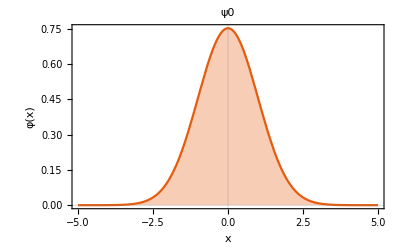
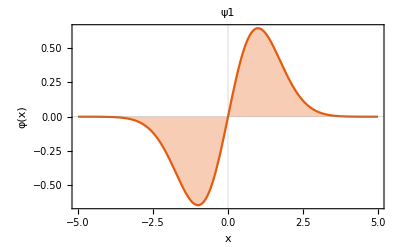
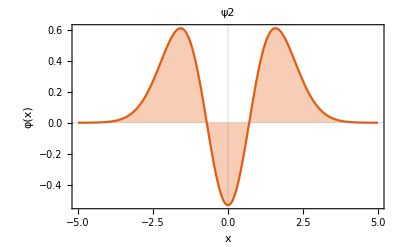

```mathematica
Table[
Plot[Evaluate[ Subscript[ψ, i] /. {m-> 1.0,ω->1.0, ℏ->1.0}],{x,-5,5},
Filling -> Axis, 
FrameLabel -> {"x", "φ(x)"},
PlotTheme ->"Scientific",
PlotLabel->"ψ"<>ToString[i]
],
{i, 0, 2}]
```

```mathematica
(* check orthogonality *)
```

```mathematica
$Assumptions = Re[(m ω)/ℏ]>0;
Integrate[Times @@ ReleaseHold @# ,{x, -Infinity, Infinity} ]&/@Permutations[Thread @ HoldForm @{ Subscript[ψ, 0],  Subscript[ψ, 1],  Subscript[ψ, 2]}, {2}]
```

{0,0,0,0,0,0}

## Griffiths 2.11

### Definitions and Assumptions

```mathematica
InnerProduct[⟨φ_, k_:1, ψ_⟩, lower_:-∞, upper_:∞]:= ∫_lower^upper (SuperStar[φ] k ψ) ⅆx
```

```mathematica
p[k_, var_]:= (ℏ/I)^k D[#, {var, k}] &;
```

```mathematica
$Assumption = m>0 && ℏ>0 && ω>0 && n ∈ Integers;
```

### Configuration Space

```mathematica
(* <x> <x^2> Subscript[σ, x] *)
```

```mathematica
{#, #2, √(#2-#^2)} & @@(InnerProduct[⟨Subscript[ψ, 0],#, Subscript[ψ, 0]⟩]&/@ {x, x^2})
```

{0,ℏ/(2 m ω),(√(ℏ/(m ω)))/(√2)}

### Momentum Space

```mathematica
(* <p> <p^2> Subscript[σ, p] *)
```

```mathematica
{#, #2, √(#2-#^2)} &@@(InnerProduct[⟨Subscript[ψ, 0], p[#, x]@Subscript[ψ, 0]⟩]&/@ {1, 2})
```

{0,(m ω ℏ)/2,(√(m ω ℏ))/(√2)}

### Uncertainty

```mathematica
(* Subscript[σ, x] Subscript[σ, p] ≥ ℏ/2 *)
```

```mathematica
lhs = Out[19][[3]]Out[20][[3]]
```

1/2 √(ℏ/(m ω)) √(m ω ℏ)

```mathematica
Refine[lhs ≥ ℏ/2]
```

```mathematica
1/2 √(ℏ/(m ω)) √(m ω ℏ)≥ℏ/2(* output should be 'True'*)
```